```mathematica
workingDirectory=NotebookDirectory[];
NotebookEvaluate[FileNameJoin[workingDirectory,"convertFrameData.nb"]];
NotebookEvaluate[FileNameJoin[workingDirectory,"exactification.nb"]];
NotebookEvaluate[FileNameJoin[workingDirectory,"inputOutput.nb"]];
```

```mathematica
(* MINIMIZATION EXAMPLES *)
{d,n}={3,13};(* Set value of d and n before running "minimizationSetup.nb" *)
NotebookEvaluate[FileNameJoin[workingDirectory,"minimizationSetup.nb"]];
```

```mathematica
(* Example usage, one shot *)
min1=MinPhiQNp[rand[],20,10];//Timing
```

{1.04894,Null}

```mathematica
min1[[1]]
PhiVar/.min1[[2]];
%//Coherence
Welch[d,n]//N
```

0.00661952191

0.650572697

0.527046

```mathematica
(* Example usage, many shot *)
(* When searching for ETFs, it's probably best to do this with p=4; there is no need for multi-stage *)
comin=1;(* best coherence achieved so far; set to large dummy value to start *)
For[i=0,i<10,i++;min1=MinPhiQNp[rand[],20,10];co1=Coherence[PhiVar/.min1[[2]]];{min,comin}=If[co1<comin,{min1,co1},{min,comin}]];//Timing//Quiet
```

{16.4751,Null}

```mathematica
min[[1]]
PhiVar/.min[[2]];
%//Coherence
```

0.00670584705

0.646057952

```mathematica
(* Example usage, two-stage with many shot first stage *)
comin=1;(* best coherence achieved so far; set to large dummy value to start *)
For[i=0,i<10,i++;min1=MinPhiQNp[rand[],20,10];co1=Coherence[PhiVar/.min1[[2]]];{min,comin}=If[co1<comin,{min1,co1},{min,comin}]];//Timing//Quiet
min=MinPhiQNp[PhiVar/.min[[2]],40,20];//Timing//Quiet
```

{19.7514,Null}

{11.8852,Null}

```mathematica
min[[1]]
PhiVar/.min[[2]];
%//Coherence
```

5.2456686073256406224×10^-7

0.6328613818975637283

```mathematica
(* Finish with Principal Axes *)
minf=MinPhiPA[PhiVar/.min[[2]],20,2000];//Timing
```

{31.5145,Null}

```mathematica
(* Goal = 0.62214387 *)
frame=PhiVar/.minf[[2]];
frame//Coherence
```

0.6279345499726259816

(-0.355197+0.126152 ⅈ | 0.488389-0.158276 ⅈ | -0.512127-0.496562 ⅈ | -0.579233-0.186836 ⅈ | 0.931085+0.18738 ⅈ | -0.459552-0.203426 ⅈ | -0.701286-0.272139 ⅈ | 0.39574+0.453704 ⅈ | 0.429653+0.00705214 ⅈ | -0.159498+0.178236 ⅈ | -0.179496+0.0936224 ⅈ | 0.153391+0.549491 ⅈ | -0.141195+0.60828 ⅈ
0.390442+0.436221 ⅈ | -0.103581+0.526028 ⅈ | -0.246732-0.346124 ⅈ | 0.404846-0.647481 ⅈ | -0.0452736-0.089305 ⅈ | 0.304811-0.054362 ⅈ | -0.382703-0.270183 ⅈ | -0.244116-0.748438 ⅈ | 0.134139-0.200834 ⅈ | -0.488799-0.547373 ⅈ | 0.296284+0.764248 ⅈ | 0.697672+0.357117 ⅈ | 0.247786-0.155743 ⅈ
-0.619612-0.362308 ⅈ | -0.36296-0.563251 ⅈ | 0.552595+0.0715021 ⅈ | -0.172613-0.129053 ⅈ | 0.223198+0.195262 ⅈ | 0.323597-0.739493 ⅈ | -0.204856+0.415586 ⅈ | 0.104391-0.0830218 ⅈ | 0.773508-0.39838 ⅈ | 0.0390131-0.634609 ⅈ | 0.437653-0.309219 ⅈ | 0.0164+0.244916 ⅈ | 0.4425-0.573237 ⅈ)

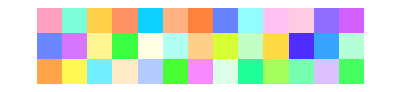

(1.+0. ⅈ | 0.424546+0.462669 ⅈ | -0.496358+0.369378 ⅈ | 0.211506-0.272548 ⅈ | -0.572755-0.239255 ⅈ | 0.300286+0.55148 ⅈ | -0.0761578-0.0851391 ⅈ | -0.53973-0.307548 ⅈ | -0.521895+0.333455 ⅈ | -0.144734+0.363666 ⅈ | 0.365487+0.5087 ⅈ | 0.344121-0.525245 ⅈ | 0.0892059+0.14836 ⅈ
0.424546-0.462669 ⅈ | 1.+0. ⅈ | -0.56888+0.127364 ⅈ | -0.500506-0.379204 ⅈ | 0.191793+0.326793 ⅈ | 0.0466557+0.123877 ⅈ | -0.561635-0.280835 ⅈ | -0.238077+0.579087 ⅈ | 0.0328189+0.601965 ⅈ | -0.000126969+0.627935 ⅈ | 0.284162+0.141042 ⅈ | -0.0403703-0.190999 ⅈ | -0.110559+0.617818 ⅈ
-0.496358-0.369378 ⅈ | -0.56888-0.127364 ⅈ | 1.+0. ⅈ | 0.409024+0.0489681 ⅈ | -0.390499+0.464684 ⅈ | 0.405915-0.436878 ⅈ | 0.598736-0.0303639 ⅈ | -0.0569283+0.0109834 ⅈ | 0.211829+0.0302685 ⅈ | 0.279422-0.558082 ⅈ | -0.0724569-0.425256 ⅈ | -0.620582+0.082294 ⅈ | -0.0334341-0.605844 ⅈ
0.211506+0.272548 ⅈ | -0.500506+0.379204 ⅈ | 0.409024-0.0489681 ⅈ | 1.+0. ⅈ | -0.598556-0.00494584 ⅈ | 0.502372+0.376728 ⅈ | 0.458784-0.428741 ⅈ | 0.0644713-0.622122 ⅈ | -0.14795+0.250324 ⅈ | 0.290775-0.556554 ⅈ | -0.324047+0.523332 ⅈ | -0.174728+0.266523 ⅈ | 0.166889-0.125277 ⅈ
-0.572755+0.239255 ⅈ | 0.191793-0.326793 ⅈ | -0.390499-0.464684 ⅈ | -0.598556+0.00494584 ⅈ | 1.+0. ⅈ | -0.547114-0.301853 ⅈ | -0.627071-0.0111642 ⅈ | 0.538463+0.321453 ⅈ | 0.508084-0.292825 ⅈ | -0.159303+0.027708 ⅈ | -0.193943-0.04181 ⅈ | 0.233788+0.58048 ⅈ | -0.0279607+0.407649 ⅈ
0.300286-0.55148 ⅈ | 0.0466557-0.123877 ⅈ | 0.405915+0.436878 ⅈ | 0.502372-0.376728 ⅈ | -0.547114+0.301853 ⅈ | 1.+0. ⅈ | -0.0979401-0.137764 ⅈ | -0.212707-0.319069 ⅈ | 0.397826+0.473326 ⅈ | 0.399718-0.48428 ⅈ | 0.482496+0.393098 ⅈ | -0.164834+0.0168455 ⅈ | 0.592237-0.200534 ⅈ
-0.0761578+0.0851391 ⅈ | -0.561635+0.280835 ⅈ | 0.598736+0.0303639 ⅈ | 0.458784+0.428741 ⅈ | -0.627071+0.0111642 ⅈ | -0.0979401+0.137764 ⅈ | 1.+0. ⅈ | -0.161247-0.0163822 ⅈ | -0.624321-0.0147669 ⅈ | 0.126578+0.022806 ⅈ | -0.437639-0.44547 ⅈ | -0.522173-0.348765 ⅈ | -0.448146-0.404917 ⅈ
-0.53973+0.307548 ⅈ | -0.238077-0.579087 ⅈ | -0.0569283-0.0109834 ⅈ | 0.0644713+0.622122 ⅈ | 0.538463-0.321453 ⅈ | -0.212707+0.319069 ⅈ | -0.161247+0.0163822 ⅈ | 1.+0. ⅈ | 0.404618-0.0200926 ⅈ | 0.603504-0.152322 ⅈ | -0.601518+0.157729 ⅈ | -0.146204+0.609777 ⅈ | 0.369962+0.50515 ⅈ
-0.521895-0.333455 ⅈ | 0.0328189-0.601965 ⅈ | 0.211829-0.0302685 ⅈ | -0.14795-0.250324 ⅈ | 0.508084+0.292825 ⅈ | 0.397826-0.473326 ⅈ | -0.624321+0.0147669 ⅈ | 0.404618+0.0200926 ⅈ | 1.+0. ⅈ | 0.260085-0.56922 ⅈ | 0.271511+0.138679 ⅈ | 0.00675949+0.619006 ⅈ | 0.578784+0.0240978 ⅈ
-0.144734-0.363666 ⅈ | -0.000126969-0.627935 ⅈ | 0.279422+0.558082 ⅈ | 0.290775+0.556554 ⅈ | -0.159303-0.027708 ⅈ | 0.399718+0.48428 ⅈ | 0.126578-0.022806 ⅈ | 0.603504+0.152322 ⅈ | 0.260085+0.56922 ⅈ | 1.+0. ⅈ | -0.304529+0.0713496 ⅈ | -0.61781+0.112308 ⅈ | 0.476114+0.398356 ⅈ
0.365487-0.5087 ⅈ | 0.284162-0.141042 ⅈ | -0.0724569+0.425256 ⅈ | -0.324047-0.523332 ⅈ | -0.193943+0.04181 ⅈ | 0.482496-0.393098 ⅈ | -0.437639+0.44547 ⅈ | -0.601518-0.157729 ⅈ | 0.271511-0.138679 ⅈ | -0.304529-0.0713496 ⅈ | 1.+0. ⅈ | 0.434991-0.428119 ⅈ | 0.407598-0.445529 ⅈ
0.344121+0.525245 ⅈ | -0.0403703+0.190999 ⅈ | -0.620582-0.082294 ⅈ | -0.174728-0.266523 ⅈ | 0.233788-0.58048 ⅈ | -0.164834-0.0168455 ⅈ | -0.522173+0.348765 ⅈ | -0.146204-0.609777 ⅈ | 0.00675949-0.619006 ⅈ | -0.61781-0.112308 ⅈ | 0.434991+0.428119 ⅈ | 1.+0. ⅈ | 0.296704-0.144032 ⅈ
0.0892059-0.14836 ⅈ | -0.110559-0.617818 ⅈ | -0.0334341+0.605844 ⅈ | 0.166889+0.125277 ⅈ | -0.0279607-0.407649 ⅈ | 0.592237+0.200534 ⅈ | -0.448146+0.404917 ⅈ | 0.369962-0.50515 ⅈ | 0.578784-0.0240978 ⅈ | 0.476114-0.398356 ⅈ | 0.407598+0.445529 ⅈ | 0.296704+0.144032 ⅈ | 1.+0. ⅈ)

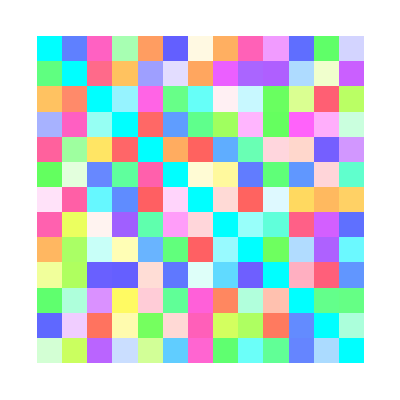

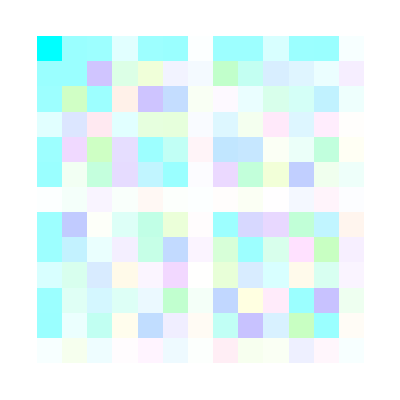
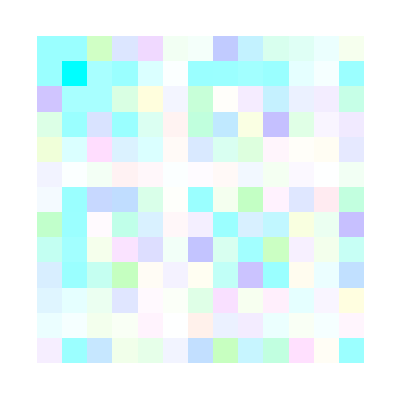
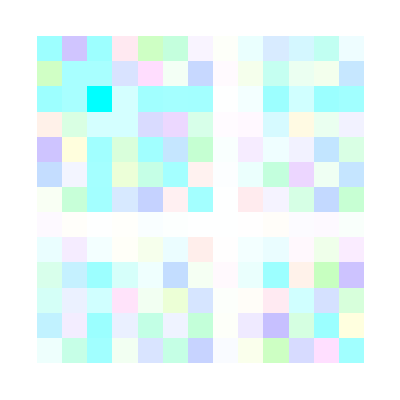
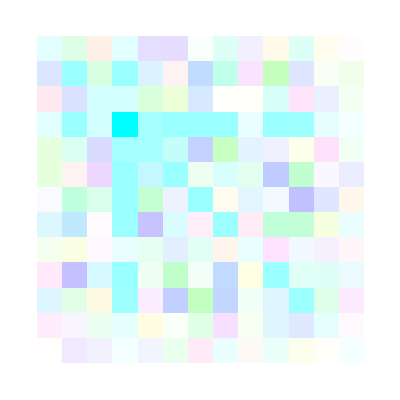
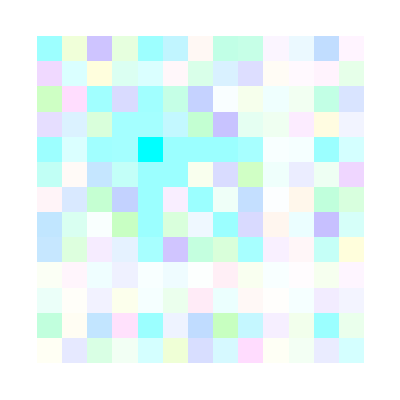
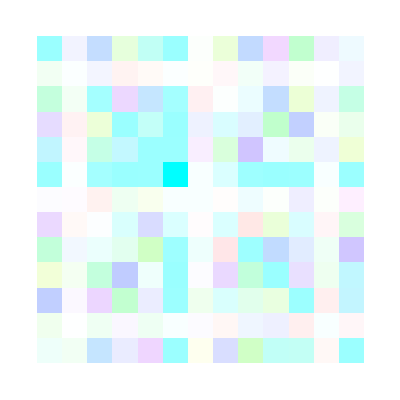
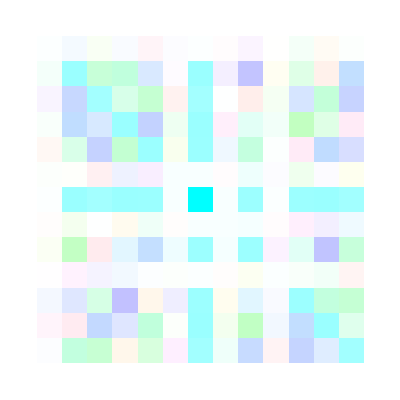

```mathematica
(* CONVERSION EXAMPLES *)
Phi=normalizeSO[frame];Phi//N//mf
Phi//FrameVisualize
G=GMfromSO[Phi];G//mf 
G//FrameVisualize
T=TPfromGM[G];
FrameVisualize/@T
```

```mathematica
(* EXACTIFICATION EXAMPLES *)
```

```mathematica
X/.NSolve[X^2-2==0,X,WorkingPrecision->10]
exactifyTuple[%]
```

{-1.414213562,1.414213562}

{-√2,√2}

```mathematica
X/.NSolve[X^2-2==0,X,WorkingPrecision->10]//Reverse
exactifyTuple[%]
```

{1.414213562,-1.414213562}

{√2,-√2}

```mathematica
arrayPositionMap[{{1,1},{1,2}}]
arrayPositionMap[{{1,1+10^(-5)},{1+10^(-10),2}}]
```

{{{1,1},{1,2},{2,1}}→1,{{2,2}}→2}

{{{1,1},{2,1}}→1,{{1,2}}→100001/100000,{{2,2}}→2}

```mathematica
X/.NSolve[X^4-(1+Sqrt[2])==0,X,WorkingPrecision->10]//Reverse
exactifyTuple[%]//FullSimplify
N[%,10]
```

{1.246504703,1.246504703 ⅈ,-1.246504703 ⅈ,-1.246504703}

{(1+√2)^(1/4),ⅈ (1+√2)^(1/4),-ⅈ (1+√2)^(1/4),-(1+√2)^(1/4)}

{1.246504703,1.246504703 ⅈ,-1.246504703 ⅈ,-1.246504703}

```mathematica
(* INPUT/OUTPUT EXAMPLES *)
```

```mathematica
(* Example import for (d,n)=(2,4) *)
etf = importPacking[2, 4, "etf_2x4_a_4.gos"];
etf // mf
GMfromSO[etf] // mf
numberTPfromSO[etf]
```

(1. | 0.577350269189626 | -0.288675134594813-0.5 ⅈ | -0.288675134594813+0.5 ⅈ
0 | 0.816496580927726 | 0.816496580927726 | 0.816496580927726)

(1. | 0.57735026918963 | -0.28867513459481-0.5 ⅈ | -0.28867513459481+0.5 ⅈ
0.57735026918963 | 1. | 0.5-0.28867513459481 ⅈ | 0.5+0.28867513459481 ⅈ
-0.28867513459481+0.5 ⅈ | 0.5+0.28867513459481 ⅈ | 1.+0. ⅈ | 0.5-0.28867513459481 ⅈ
-0.28867513459481-0.5 ⅈ | 0.5-0.28867513459481 ⅈ | 0.5+0.28867513459481 ⅈ | 1.+0. ⅈ)

4

```mathematica
(* EXACTIFICATION OF ETF EXAMPLE *)
```

```mathematica
Phiapprox = importPacking[2, 4, "etf_2x4_a_4.gos"];
Tapprox=TPfromSO[Phiapprox];
Texact=exactifyTP[Tapprox];
SOexact=SOfromTP[Texact]//FullSimplify;
SOexact//mf
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/3+(-1/(2 √3)+(√3)/2)/(√3).

General::stop: Further output of N::meprec will be suppressed during this calculation.

((ⅈ+√3)/(√6) | ⅈ/(√2)+1/(√6) | 0 | √(2/3)
1/(√3) | -ⅈ/(√3) | 1 | ⅈ/(√3))